```mathematica
Limit[(x-Tan[x])/x, {x->0}]
```

{0}

```mathematica
D[(x-Tan[x]), x]
```

1-Sec[x]^2

```mathematica
D[x-Tan[x],x]
```

1-Sec[x]^2

```mathematica
Limit[(x-Tan[x])/x, {x->0}]->Limit[D[(x-Tan[x]), x]/D[x, x],{x->0}] ->Limit[(1-Sec[x]^2)/1,{x->0}] ->0
```

{0}→{0}→{0}→0

```mathematica
f2[x_]:= 1 /;0≤ x < 1
```

```mathematica
f2[x_]:= 0 /; 1≤x≤2
```

```mathematica
x=1
```

1

```mathematica
0≤ x < 1
```

False

```mathematica
x=0
```

0

```mathematica
0≤ x < 1
```

True

```mathematica
Clear[x]
```

```mathematica
Clear[f]
```

```mathematica
f[x]:=2x
```

```mathematica
f[0]
```

f[0]

```mathematica
x=0
```

0

```mathematica
f2[x]
```

1

```mathematica
f3[x_]:= 1 /;0≤ x < 1
```

```mathematica
f3[x_]:= 0 /; 1≤x≤2
```

```mathematica
f3[0]
```

1

```mathematica
f3[1]
```

0

```mathematica
f3[3]
```

f3[3]

```mathematica
x=0
```

0

```mathematica
f3[x]
```

1

```mathematica
Clear[x]
```

```mathematica
f3[x]
```

f3[x]

```mathematica
f3[x-1]
```

f3[-1+x]

```mathematica
f3[x]/;1≤x<2
```

f3[x]/;1≤x<2

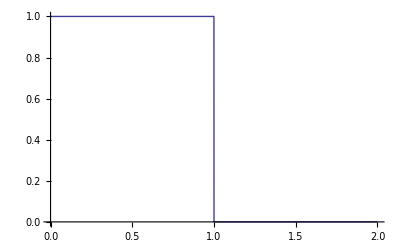

```mathematica
Plot[f3[x], {x,0,2}]
```

```mathematica
f3[0.08113398314583158]
```

1

```mathematica
Assuming[f'[Subscript[x, 0]]==3, Limit[(f[Subscript[x, 0]-2h]-f[Subscript[x, 0]])/h,{h->0}]]
```

{Limit[(-f[x_0]+f[-2 h+x_0])/h,h→0]}

```mathematica
y[x_]= ArcTan[ⅇ^x]
```

ArcTan[ⅇ^x]

```mathematica
y'[x]->Dt[ArcTan[ⅇ^x]]/Dt[ⅇ^x] * D[ⅇ^x,x]
```

ⅇ^x/(1+ⅇ^(2 x))→ⅇ^x/(1+ⅇ^(2 x))

```mathematica
D[y[x], x]
```

ⅇ^x/(1+ⅇ^(2 x))

```mathematica
Dt[ArcTan[ⅇ^x]]
```

(ⅇ^x Dt[x])/(1+ⅇ^(2 x))

```mathematica
D[Tan[x],x]
```

Sec[x]^2

```mathematica
D[Cot[x],x]
```

-Csc[x]^2

```mathematica
D[ArcCot[x],x]
```

-1/(1+x^2)

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

```mathematica
D[ArcSin[x],x]
```

1/(√(1-x^2))

```mathematica
D[ArcCos[x],x]
```

-1/(√(1-x^2))

```mathematica
Clear[y]

RSolve[y[x]==Sin[x+y[x]],y[x],x]
```

Solve[Sin[x+y[x]]-y[x]==0,y[x]]

```mathematica
{{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
MatrixForm[{{1,2,3},{4,5,6},{7,8,9}}]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

This is a text contains Formular ∫y[x]ⅆx.

```mathematica
TeXForm[∫y[x]ⅆx]
```

\int y(x) \, dx

```mathematica
TeXForm[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})]
```

\left(
\begin{array}{ccc}
 1 & 2 & 3 \\
 4 & 5 & 6 \\
 7 & 8 & 9
\end{array}
\right)

```mathematica
y==Sin[x+y]
```

y==Sin[x+y]

```mathematica
y'[x]== (ⅆ(Sin[x+y[x]]))/(ⅆ(x+y[x]))*(ⅆ(x+y))/ⅆx -> y'[x]==Cos[x+y[x]]*(1+y'[x])
```

y'[x]==(ⅆ(x+y) ⅆSin[x+y[x]])/(ⅆx ⅆ(x+y[x]))→y'[x]==Cos[x+y[x]] (1+y'[x])

```mathematica
y+x==Sin[x+y]+x ->
(ⅆ(x+y))/(ⅆ(x+y)) == (ⅆ(Sin[x+y]))/(ⅆ(x+y))+ⅆx/(ⅆ(x+y)) ->
y'[x] + 1
```

x+y==x+Sin[x+y]→1==ⅆx/(ⅆ(x+y))+ⅆSin[x+y]/(ⅆ(x+y))→1+y'[x]

```mathematica
Clear[x]
```

```mathematica
Clear[y]
```

```mathematica
D[y,x] /. y->Sin[x+y[x]]
```

0

```mathematica
DSolve[y'[x]==x, y[x], x]
```

{{y[x]→x^2/2+C[1]}}

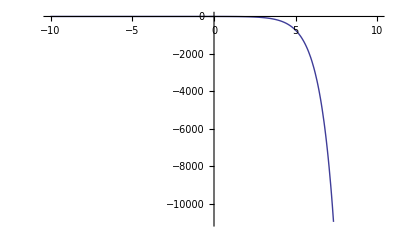

```mathematica
Plot[1-x ⅇ^x, {x,-10,10}]
```

```mathematica
y[x_]=1-x ⅇ^x
```

1-ⅇ^x x

```mathematica
y'[0]
```

-1

```mathematica
Limit[x*(π/2-ArcTan[x]), {x->+∞}]
```

{1}

```mathematica
Limit[ArcTan[x], {x->+∞}]
```

{π/2}

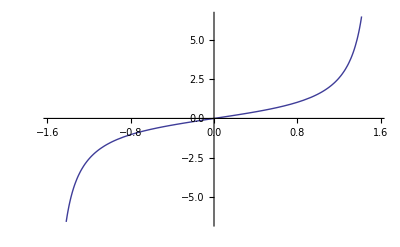

```mathematica
Plot[Tan[x],{x, -π/2,π/2}]
```

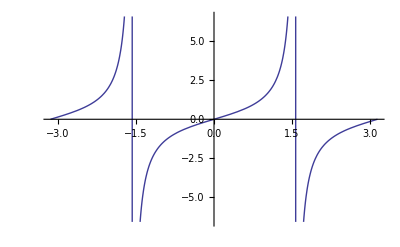

```mathematica
Plot[Tan[x],{x, -π,π}]
```

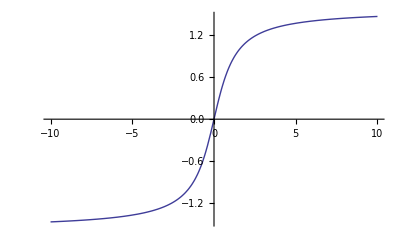

```mathematica
Plot[ArcTan[x],{x, -10,10}]
```

```mathematica
Limit[x*(π/2-ArcTan[x]), {x->+∞}] -> 
Limit[(π/2-ArcTan[x])/(1/x), {x->+∞}] -> 
Limit[D[(π/2-ArcTan[x]), x]/D[1/x,x],  {x->+∞}]->
Limit[(-1/(1+x^2))/(-1/x^2),  {x->+∞}]->
Limit[x^2/(1+x^2),  {x->+∞}]->
Limit[1/(1+1/x^2),  {x->+∞}]
```

{1}→{1}→{1}→{1}→{1}→{1}

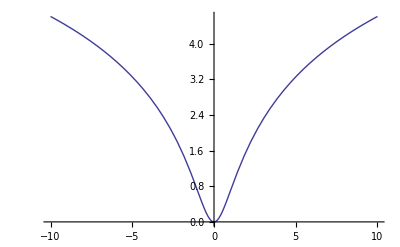

```mathematica
Plot[Log[1+x^2], {x, -10,10}]
```

```mathematica
D[Log[1+x^2],x]
```

(2 x)/(1+x^2)

```mathematica
Clear[y]
Clear[x]
(D[Log[y[x]],y[x]]*D[y[x],x] )/. y[x]->1+x^2
```

y'[x]/(1+x^2)

```mathematica
49+10+7+5+4+21
```

96

```mathematica
The story of ⅈ
```

ⅈ of story The

```mathematica
TraditionalForm[Solve[x^3+px ==q, x]]
```

{{x→(q-px)^(1/3)},{x→--1^(1/3) (q-px)^(1/3)},{x→(-1)^(2/3) (q-px)^(1/3)}}

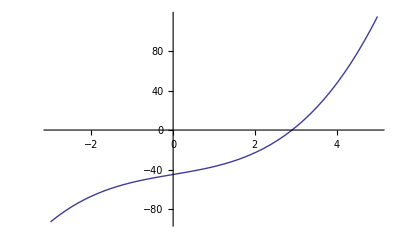

```mathematica
Plot[x^3+7x-45, {x, -3, 5}]
```

```mathematica
Simplify[Cos[x]^3-3/4 Cos[x]-1/4 Cos[3x]]
```

0

复数时间赶上车,实部是最近值.
ABC共线, AP垂直AC, PB垂直AC·BP = √(AB·BC), 已知AP,PB,角PAD

```mathematica
Simplify[ArcTan[1/2]+ArcTan[1/3]-π/4]
```

-π/4+ArcTan[1/3]+ArcTan[1/2]

```mathematica
(Cos[x]+ⅈSin[x])^-1==Cos[x]-ⅈSin[x]
```

1/(Cos[x]+ⅈSin[x])==Cos[x]-ⅈSin[x]

```mathematica
ⅇ^ⅈx==Cos[x]+ⅈSin[x]
```

ⅇ^ⅈx==Cos[x]+ⅈSin[x]

```mathematica
ⅇ^ⅈπ==-1
```

ⅇ^ⅈπ==-1

```mathematica
ⅈ^ⅈ==ⅇ^(-π/2)
```

True

```mathematica
Series[ⅇ^x,{x, 0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Series[ⅇ^ⅈx,{x, 0,10}]
```

ⅇ^ⅈx

```mathematica
Series[Sin[x]/x,{x, 0,10}]
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880-x^10/39916800+O[x]^11

```mathematica
Subscript[S, p]=∑_(n=1)^∞ 1/n^p
```

Zeta[p]

```mathematica
TraditionalForm[Zeta[p]]==ζ[p]
```

p==ζ[p]

```mathematica
ζ[p]
```

ζ[p]

```mathematica
Series[Log[1+x],{x, 0,10}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+O[x]^11

```mathematica
Series[Sin[√x]/(√x),{x, 0,10}]
```

1-x/6+x^2/120-x^3/5040+x^4/362880-x^5/39916800+x^6/6227020800-x^7/1307674368000+x^8/355687428096000-x^9/121645100408832000+x^10/51090942171709440000+O[x]^(21/2)

```mathematica
N[γ]
```

γ

```mathematica
∑_(p=2)^∞ (-1)^p/p(∑_(p=2)^∞ 1/n^p)
```

(1-Log[2])/((-1+n) n)

π[x]==不大于x的素数个数

```mathematica
∫_2^x 1/Log[u] ⅆu==li[x]
```

ConditionalExpression[-LogIntegral[2]+LogIntegral[x]==li[x],Re[x]≥1||x∉Reals]

```mathematica
∑_(n=1)^∞ (-1)^(n+1)/n^z+2∑_(n=1)^∞ 1/(2n)^z
```

2^(-6 x^2+2 x^3-6 x y-3 y^2) Zeta[1+6 x^2-2 x^3+6 x y+3 y^2]+2^(-6 x^2-6 x y-3 y^2) (-2^(2 x^3)+2^(6 x^2+6 x y+3 y^2)) Zeta[1+6 x^2-2 x^3+6 x y+3 y^2]

1^π==Cos[2 π^2 n]+ⅈSin[2 π^2 n],where N=0, ±1,±2

```mathematica
Simplify[Γ[N+1]/Γ[N]]==N
```

Γ[1+N]/Γ[N]==N

```mathematica
∫_0^∞ e^-x x^(n-1)ⅆx /;n>0
```

ConditionalExpression[Gamma[n] Log[e]^-n,Re[Log[e]]>0&&Re[n]>0]/;n>0

```mathematica
Γ[1-N]Γ[N]==π/Sin[N x]
```

Γ[1-N] Γ[N]==π Csc[N x]

```mathematica
ζ[s]==ζ[1-s]Γ[1-s] 2^s π^(s-1)Sin[1/2 πs]
```

ζ[s]==2^s π^(-1+s) Sin[πs/2] Γ[1-s] ζ[1-s]

解析函数必然满足拉普拉斯方程.柯西第一积分原理.格林定理.第二with极点

```mathematica
Limit[ⅇ^(1/(1-(1-1/10^n))), n->+∞]
```

∞

```mathematica
Limit[ⅇ^(1/(1-1/10^n)-1), n->+∞]
```

1